Initialization Cells. (scroll down to run simulation)

```mathematica
SetDirectory[NotebookDirectory[]<>"/../"];
<<SimulationRewardDriven4`;
SetDirectory[NotebookDirectory[]];
(*displays results of simulation*)
PlotBelief1[]:=Module[
{plot,plotforrange1,plotforrange2,data,size},
data=Table[Mean/@BELIEF[[i]],{i,1,BELIEF//Length}];
size=(Length/@data)//Max;
size=nquestionsUSER;
plot=data//ListLinePlot[#,AxesLabel->{Style["j",Large],Style["d",Large]},PlotRange->All,PlotLegends->Table[Style["a= "<>ToString[AffinityValues[[i]]]<>", b="<>ToString[BiasValues[[i]]],Large],{i,1,AffinityValues//Length}],ImageSize->Large,TicksStyle->Directive["Label", 20]]&;
plotforrange1=ListLinePlot[{Join[ConstantArray[-dMAX-0.5,size-1],ConstantArray[dMAX+0.5,1]]},ImageSize->Large,TicksStyle->Directive["Label", 20],PlotStyle->None];
Print["size=",size];
Show[plotforrange1,plot]
]

markerphase[in_:GrayLevel[0],out_:GrayLevel[0],size_:7]:=Graphics[{in,EdgeForm[{AbsoluteThickness[1],out}],Disk[]},PlotRangePadding->0,ImageSize->size]
marker[d_]:=Module[
{DMAX=dMAX,DMIN=-dMAX,opacity=0.08},
d//Which[
#==DMAX,markerphase[Opacity[opacity,ColorData["VisibleSpectrum",470]],ColorData["VisibleSpectrum",470],15*Sqrt[Abs[#]]],
#==DMIN,markerphase[Opacity[opacity,ColorData["VisibleSpectrum",630]],ColorData["VisibleSpectrum",630],15*Sqrt[Abs[#]]],
DMAX>#>0,markerphase[Transparent,ColorData["VisibleSpectrum",470],15*Sqrt[Abs[#]]],
DMIN<#<0,markerphase[Transparent,ColorData["VisibleSpectrum",630],15*Sqrt[Abs[#]]],
#==0,markerphase[Opacity[opacity,Black],Black,10],
#===666,"",
True,Style["☒",RGBColor[1, 0, 1],Large]
]&
]


marker2[{d_,reachedstopcond_}]:=Module[
{DMAX=dMAX,DMIN=-dMAX,opacity=0.1,opacityline=0.3,
sizemin=4,sizeinc=8
},
red=640;
purple=450;
darkblue=475;
d//Which[
reachedstopcond,
#//Which[
DMAX≥ #>0,markerphase[Opacity[opacity,ColorData["VisibleSpectrum",darkblue]],(*ColorData["VisibleSpectrum",480]*)Transparent,sizemin+sizeinc Sqrt[Abs[#]]],
DMIN≤ #<0,markerphase[Opacity[opacity,ColorData["VisibleSpectrum",red]],(*ColorData["VisibleSpectrum",625]*)Transparent,sizemin+sizeinc Sqrt[Abs[#]]],
#==0,markerphase[Opacity[opacity,Transparent],Black,2 sizemin],
#===666,"",
True,Style["☒",RGBColor[1, 0, 1],Large]
]&,

True,
#//Which[
DMAX≥ #>0,markerphase[Transparent,Opacity[opacityline,ColorData["VisibleSpectrum",darkblue]],sizemin+sizeinc Sqrt[Abs[#]]],
DMIN≤ #<0,markerphase[Transparent,Opacity[opacityline,ColorData["VisibleSpectrum",red]],sizemin+ sizeinc Sqrt[Abs[#]]],
#==0,markerphase[Transparent,Opacity[1.0,Black],2 sizemin],
#===666,"",
True,Style["☒",RGBColor[1, 0, 1],Large]
]&

]&
]

PhasePlot[{biasaffpair_,BeliefFinal_},label_]:=Module[
{meanconclusion,markertable,invisible,range,biasaffpairPADDED,meanconclusionPADDED},
meanconclusion=Mean/@BeliefFinal;
meanconclusionPADDED=Join[{666,666},meanconclusion];
markertable=marker/@(meanconclusionPADDED);

invisible={{{bMIN,aMIN}},{{bMAX,aMAX}}};
range={{aMIN,aMAX},{bMIN,bMAX}};
biasaffpairPADDED=Join[invisible,List/@biasaffpair];
(*Print["plot range: ",invisible];*)

(Reverse[#,2]&/@biasaffpairPADDED)//ListPlot[#,PlotMarkers->markertable,PlotRange->range,ImageSize->500,LabelStyle->Directive[Bold, 16],FrameLabel->{Style["a",Bold,Large],Style["b",Bold,Large]},PlotLabel->label,PlotStyle->Thick,AspectRatio->0.9,Frame->True,ImageMargins->25]&

]

PhasePlot2[BELIEF_List,PHASE_List,label_,message_:True]:=Module[
{reachedstopcond,meanconclusion,meanconclusionstop,markertable,invisible,range,range2,biasaffpair=PHASE[[1]],biasaffpairPADDED,meanconclusionstopPADDED,plot1,plot2,amin,amax,bmin,bmax,fontsize,fontcolor},

If[
message//TrueQ,
Print[Style["WARNING: ",Bold,Orange,Medium]," Using nquestions=",nquestions," to verify stop condition."],
Nothing
];

reachedstopcond=#<nquestions&/@(Length/@BELIEF);
meanconclusion=Mean/@BELIEF[[All,-1]];
meanconclusionstop={meanconclusion,reachedstopcond}//Transpose;

meanconclusionstopPADDED=Join[{{666,True},{666,True}},meanconclusionstop];
markertable=marker2/@(meanconclusionstopPADDED);
(*Print[markertable];*)

amin=PHASE[[1,All,2]]//Min;
amax=PHASE[[1,All,2]]//Max;
bmin=PHASE[[1,All,1]]//Min;
bmax=PHASE[[1,All,1]]//Max;

(*extend ranges a bit, for visibility*)
amin=amin-(amax-amin)0.05;
amax=amax+(amax-amin)0.05;
bmin=bmin-(bmax-bmin)0.05;
bmax=bmax+(bmax-bmin)0.05;

invisible={{{bmin,amin}},{{bmax,amax}}};
range={{bmin,bmax},{amin,amax}};
range2=range//Reverse;
biasaffpairPADDED=Join[invisible,List/@biasaffpair];

(*plot1=(biasaffpairPADDED)//ListPlot[#,PlotMarkers->markertable,PlotRange->range,ImageSize->500,LabelStyle->Directive[Bold, 16],FrameLabel->{Style["b",Bold,Large],Style["a",Bold,Large]},PlotLabel->label,PlotStyle->Thick,AspectRatio->0.9,Frame->True,ImageMargins->25]&;*)

fontsize=28;
fontcolor=Black;

plot2=(Reverse[#,2]&/@biasaffpairPADDED)//ListPlot[#,PlotMarkers->markertable,PlotRange->range2,ImageSize->650,LabelStyle->Directive[ fontcolor,fontsize],TicksStyle->Directive[fontcolor,fontsize],FrameLabel->{Style["a_0",fontcolor,fontsize],Style["b",fontcolor,fontsize]},PlotLabel->Style[label,fontsize],PlotStyle->Thick,AspectRatio->0.9,Frame->True,ImageMargins->25]&;

plot2

]

GetPHASEq[qmax_]:=Module[
(*snapshot at qmax *)
{length,maxlength,lengtheff,PHASEq},
length=Table[BELIEF[[i]]//Length,{i,1,BELIEF//Length}];
maxlength=Max[length];
lengtheff=Which[#<qmax,#,True,qmax]&/@length;

If[maxlength≤qmax,
Print[Style["\nWarning: ",Orange,16,Bold],Style["requested qmax =" <>ToString[qmax]<>" is larger or equal to the largest nquestions asked = "<>ToString[maxlength]<>" in simulation. No cut has been done.",16,Bold]];
];

PHASEq={PHASE[[1]],Table[BELIEF[[i,lengtheff[[i]]]],{i,1,BELIEF//Length}]}
]

indexGetBELIEFq[qnumber_,l_]:=Which[qnumber≤l,qnumber,True,-1];

GetBELIEFq[qmax_]:=Module[
{length,
stopcondition,
BELIEFq,
maxlength},
length=(Length/@BELIEF);
maxlength=Max[length];
stopcondition=#<qmax&/@length;

If[maxlength≤qmax,
Print[Style["\nWarning: ",Orange,16,Bold],Style["requested qmax =" <>ToString[qmax]<>" is larger or equal to the largest nquestions asked = "<>ToString[maxlength]<>" in simulation. No cut has been done.",16,Bold]];
];

BELIEFq=Table[BELIEF[[i,1;;indexGetBELIEFq[qmax,length[[i]]]]],{i,1,BELIEF//Length}]

]

PhasePlotq[qmax_,label_,fname_:False]:=Module[
{nquestionsold=nquestions,PHASEq,BELIEFq,plot}, 
nquestions=qmax;
PHASEq=GetPHASEq[qmax];
BELIEFq=GetBELIEFq[qmax];
plot=PhasePlot2[BELIEFq,PHASEq,label];
nquestions=nquestionsold;

If[
TrueQ[!fname],
Nothing,
Export[fname,plot];
plot=Import[fname][[1]];
];
plot
]


INFO[]:=Module[
{info=""},
info=info<>"dinit = "<>ToString[d]<>"\n";
info=info<>"hinit = "<>ToString[h]<>"\n";
info=info<>"nquestions = "<>ToString[nquestions]<>"\n";
info=info<>"nexperiments = "<>ToString[nexperimentsUSER]<>"\n";
info=info<>"npredictors = "<>ToString[npredictors]<>"\n";
info=info<>"RTHRESHOLD = "<>ToString[RTHRESHOLD]<>"\n";
info=info<>"R0 = "<>ToString[R0]<>"\n";
info=info<>"B0 = "<>ToString[B0]<>"\n";
info=info<>INFOPREDICTIVEPOWER;

info

]


SaveSimulation[id_String]:=Module[
{dir=id,names="",out,info=""},
(*saves superarrays*)
(*names=SUPERARRAYNAME//DeleteCases["PLOTS"];
out=(Export[dir<>"/"<>#,#//ToExpression,"String"]&)/@names;
Print/@out;*)
(*saves phase space data*)
Export[dir<>"/"<>"PHASE",PHASE,"String"];
(*saves BELIEF  data*)
Export[dir<>"/"<>"BELIEF",BELIEF,"String"];
(*saves initital d, h arrays and ranges aMIN,aMAX and bMIN,bMAX, and other values for the simulation.*)
Export[dir<>"/"<>"info",INFO[],"String"];

]
LoadSimulation[id_String,printplot_:True]:=Module[
{dir=id,names="",out,pts1,pts2,label},
(*loads superarrays*)
(*names=SUPERARRAYNAME//DeleteCases["PLOTS"]//DeleteCases["EXPERIMENT"];
names={"CREWARD"};
Unprotect/@names;
out=(#<>"=Import[\""<>dir<>"/"<>#<>"\"]//ToExpression"//ToExpression)&/@names;*)
(*loads phase space data*)
PHASE=Import[dir<>"/PHASE"]//ToExpression;
(*loads BELIEF data, WARNING: overrides current value of BELIEF*)
BELIEF//Unprotect;
BELIEF=Import[dir<>"/BELIEF"]//ToExpression;
BELIEF//Protect;
(*prints contents of info file*)
InfoCurrent=Import[dir<>"/info"];Print[InfoCurrent];
(*plot phase diagram*)
pts1=PHASE[[1]]//Length;
pts2=BELIEF//Length;
If[printplot,
label=Which[pts1==pts2,id<>": pts = "<>ToString[pts1],True,id<>": pts1 = "<>ToString[pts1]<>",  pts2 = "<>ToString[pts2]];
PhasePlot2[BELIEF,PHASE,label],
Nothing
];
]

LoadSimulationAll[pattern_String]:=Module[
{phasefull={},belieffull={},simulationids,it},
simulationids=FileNames[pattern];
For[
it=1,it≤(simulationids//Length),it++,
Print[Style["Loading '"<>simulationids[[it]]<>"'. ",Bold,Blue,Medium]];
LoadSimulation[simulationids[[it]],False];
phasefull=Join[phasefull,PHASE//Transpose];
belieffull=Join[belieffull,BELIEF];
Print[Style["phasefull size = "<>ToString[phasefull//Length],Bold,Blue,Medium]];
];
Unprotect[BELIEF];BELIEF=belieffull;Protect[BELIEF];
PHASE=phasefull//Transpose;
]


SimulationExists[id_String]:=Module[
{exists},
exists=DirectoryQ[id];
exists//TrueQ
]

(*warning: deletes current values of BELIEF, PHASE, BiasAffPair and  *)
RunSimulation[id_String,NSIMULATIONS_Integer]:=Module[
{tempplot,templine,templine0,phase,id2,fullid,IT,itregions,it,amin,amax,bmin,bmax,
check1={},
BiasAffPair={},BeliefFinal={},a,b,AffinityValues={},BiasValues={}
},

For[IT=1,IT≤NSIMULATIONS,IT++,
SeedRandom[];
id2=ToString[IT];
fullid=id<>"_"<>id2;
tempplot=0;
BELIEF//Unprotect;
BELIEF={};
BELIEF//Protect;
PHASE={};
BiasAffPair={};BeliefFinal={};AffinityValues={};BiasValues={};
If[SimulationExists[fullid],Print["Simulation '"<>fullid<>"' exists. Aborting."],
SaveSimulation[fullid];
For[itregions=1,itregions≤(nregions),itregions++,
(*sets range of a and b for current region*)
{{amin,amax},{bmin,bmax}}=REGION[[itregions]];
NotebookDelete[templine0];
NotebookDelete[tempplot];
templine0=PrintTemporary[Style["region=",Large,Bold],Style[itregions,Large,Bold],
Style[" (out of "<>ToString[nregions]<>")",Large,Bold]];
tempplot=PrintTemporary[phase];

For[it=1,it≤ptsREGION,it++,
(*to show progress*)
NotebookDelete[templine];
templine=PrintTemporary[Style["it=",Large,Bold],Style[it,Large,Bold]];
(*sets and stores values of a,b for all iterations*)
a=ConstantArray[RandomReal[{amin,amax}],npredictors];
b=ConstantArray[RandomReal[{bmin,bmax}],npredictors];
AppendTo[AffinityValues,a//Mean];
AppendTo[BiasValues,b//Mean];
(*initialize experiment*)
InitExperimentRewardDriven[d,a,b,h];
(*run experiment*)
RunExperimentStop[];
(*saves data on degree of belief during the simulation*)
StoreBeliefCurrent[];
(*store values for phase plot*)
BiasAffPair=Table[{BiasValues[[i]],AffinityValues[[i]]},{i,1,AffinityValues//Length}];
BeliefFinal=Table[BELIEF[[i,-1]],{i,1,BELIEF//Length}];
PHASE={BiasAffPair,BeliefFinal};
phase=PhasePlot2[BELIEF,PHASE,"j="<>ToString[it],False];
If[Mod[it,10]==0||it==1,NotebookDelete[tempplot];tempplot=PrintTemporary[phase]];

If[
Mod[it,30]==0,
SaveSimulation[fullid],
Nothing,Nothing
]

];
SaveSimulation[fullid];
(*check1*)
EXPERIMENT//Flatten//Cases[x_:>x/;!NumericQ[x]];
AppendTo[
check1,
List[Style["This should print a value of 0: value =  ",Large,Bold,Black],Style[%//Length//ToString,Bold,Large,Blue]]
];
Init[];
];
SaveSimulation[fullid]
];
check1//DeleteDuplicates//MatrixForm//Print
];
BELIEF//Unprotect;
BELIEF={};
BELIEF//Protect;
PHASE={};
]

nquestionsUSER=1000;
nexperimentsUSER=600;
npredictorsUSER=20;
(*affinity related settings, keep fixed*)
RTHRESHOLD=4.04;
NSTABLE=4;
R0=50;
(*bias related settings*)
B0=0.7;
(*set forecast: dmax=4,nsteps=8, max power= 21 ⟹ max{Subscript[p, avg]} = 0.9545 , keep fixed *)
BuildPredictivePowerFunction[4,8];

(*unused but needed for function below 'InitSimulationRewardDriven'*)
a=ConstantArray[0,npredictorsUSER];(*a here means a0 in draft*)
b=ConstantArray[0,npredictorsUSER];

(*initial degree of belief and random walk parameter h*)
d={4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4};
h=ConstantArray[0.99,npredictorsUSER];
```

ν values = {1.,1.58824,2.66667,5.28571,21.}

ν values = {1.,1.58824,2.66667,5.28571,21.}

Load Simulation.
The argument of ‘LoadSimulationAll’ is a string pattern. Results of all simulations inside directories corresponding to the pattern are combined. 
ex1:  LoadSimulationAll[“case_I_1_1”] loads only results in directory “case_I_1_1”
ex2:  LoadSimulationAll[“case_I_1_*”] loads all results in directories which names start with “case_I_1”

```mathematica
LoadSimulationAll["case_I_1_1"];
```

Loading 'case_I_1_1'.

dinit = {4, 4, 4, 4, 4, 4, 4, 4, 4, 4, -4, -4, -4, -4, -4, -4, -4, -4, -4, -4}
hinit = {0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99, 0.99}
nquestions = 1000
nexperiments = 600
npredictors = 20
RTHRESHOLD = 4.04
R0 = 50
B0 = 0.7
######## predictive power function genereted by calling: 'BuildPredictivePowerFunction[4,8]'
dMAX = 4
dSTEPS = 8
dSTEPSIZE = 1
forecastavgMAX = 0.954545
PowerValues = {1., 1.58824, 2.66667, 5.28571, 21.}
forecastavg = {0.0454545, 0.159091, 0.272727, 0.386364, 0.5, 0.613636, 0.727273, 0.840909, 0.954545}

phasefull size = 600

Plot results.
after loading, two variables  contain all results stored:
1)‘PHASE’
2) ‘BELIEF’
which are used for the plots. To plot run :

i) PhasePlotq[j,label]: j is the question number for which the “snapshot” is taken (at most j=nmax=1000)
                                              label is a string to show in the header of the plot

iI) PhasePlotq[j,label,fname]: j and label as before, this version stores the result in a file called ‘fname’ 
                                                             (fname must have pdf extension)
Warnings are printed by default in all cases, to indicate the value of j used.

WARNING:  Using nquestions=500 to verify stop condition.

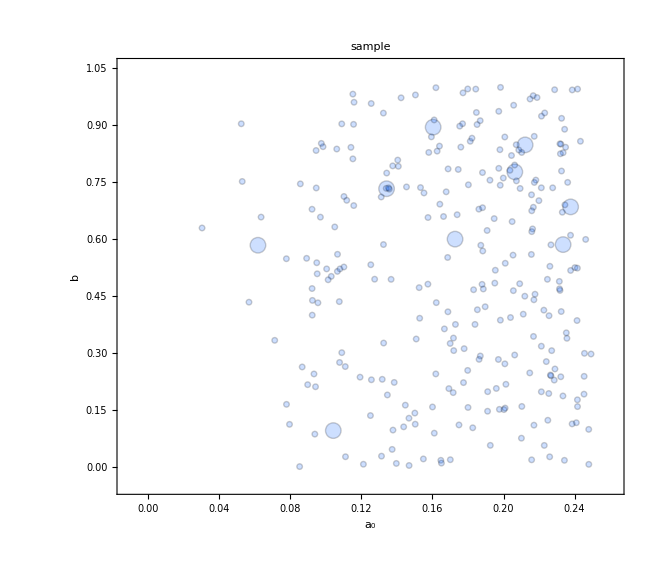

```mathematica
plot=PhasePlotq[500,"sample"]
```

```mathematica
Export["new",plot,PDF]
```